```mathematica
ClearAll["Global`*"];
(*Solve[{
(a+b)^2+((c(a+b))/a)^2==M^2,
(a+b)^2+((c(a+b))/b)^2==L^2
},{a,b}]//Simplify*)
c=(a √(M^2-(a+b)^2))/(a+b);
c=(b √(L^2-(a+b)^2))/(a+b);
a^2(M^2-(a+b)^2)^2==b^2(L^2-(a+b)^2)^2;
(*Solve[a^2(M^2-(a+b)^2)^2==b^2(L^2-(a+b)^2)^2,b]*)
b=-a+(2^(1/3) L^2)/((-27 a L^2+27 a M^2+√(-108 L^6+(-27 a L^2+27 a M^2)^2))^(1/3))+((-27 a L^2+27 a M^2+√(-108 L^6+(-27 a L^2+27 a M^2)^2))^(1/3))/(3 2^(1/3));

y1[x_]:=c/a x;
y2[x_]:=-c/b x+(c(a+b))/b;
Solve[y1[x]==y2[x],x]//Simplify

{L,M}={30,40};

a=20;
N[b]
N[c]
```

{{x→a}}

15.9141

0.+8.74879 ⅈ

```mathematica
ClearAll["Global`*"];
Solve[{(a+b)^2+((c(a+b))/a)^2==M^2},{c}]//Simplify
c=(a √(M^2-(a+b)^2))/(a+b);
ClearAll["Global`*"];
Solve[{(a+b)^2+((c(a+b))/b)^2==L^2},{c}]//Simplify
c=(b √(L^2-(a+b)^2))/(a+b);
ClearAll["Global`*"];
a √(M^2-(a+b)^2)==b √(L^2-(a+b)^2);
a^2(M^2-(a+b)^2)^2==b^2(L^2-(a+b)^2)^2;
```

{{c→-(√(-a^2-2 a b-b^2+M^2))/(√((a+b)^2/a^2))},{c→(√(-a^2-2 a b-b^2+M^2))/(√((a+b)^2/a^2))}}

{{c→-(√(-a^2-2 a b-b^2+L^2))/(√((a+b)^2/b^2))},{c→(√(-a^2-2 a b-b^2+L^2))/(√((a+b)^2/b^2))}}

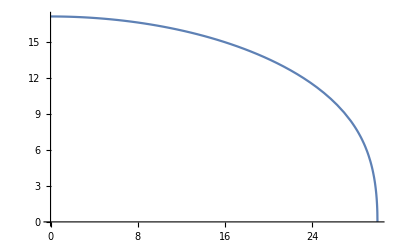

9.99989

```mathematica
ClearAll["Global`*"];
h1=√(x^2-d^2);
h2=√(y^2-d^2);
c=(h1*h2)/(h1+h2);
{x,y}={30,40};(* c =10 *)
d=26.033;
Plot[c,{d,0,30}]
N[c]
```